```mathematica
(* Mathematica*)
<<ComputationalGeometry`
```

```mathematica
Clear[r,phi,pa,pts]
```

```mathematica
(*V=12,F=11,E=21:V+F-2=21*)
```

```mathematica
N[1/(1-(5/6+1/21))]
```

8.4

```mathematica
(*Triangle group:{2,3,8.4,21}*)
```

```mathematica
p1=Table[N[{Cos[2*Pi*i/3+Pi/6],Sin[2*Pi*i/3+Pi/6],1/2}],{i,3}]/1.118033988749895
```

{{-0.774597,0.447214,0.447214},{0.,-0.894427,0.447214},{0.774597,0.447214,0.447214}}

```mathematica
max=Max[Norm/@p1]
```

1.

```mathematica
p2=Table[N[{Cos[2*Pi*i/6],Sin[2*Pi*i/6],0}],{i,6}]
```

{{0.5,0.866025,0.},{-0.5,0.866025,0.},{-1.,0.,0.},{-0.5,-0.866025,0.},{0.5,-0.866025,0.},{1.,0.,0.}}

```mathematica
max=Max[Norm/@p2]
```

1.

```mathematica
p3=Table[N[{Cos[2*Pi*i/3+Pi/6],Sin[2*Pi*i/3+Pi/6],-1/2}],{i,3}]/1.118033988749895
```

{{-0.774597,0.447214,-0.447214},{0.,-0.894427,-0.447214},{0.774597,0.447214,-0.447214}}

```mathematica
max=Max[Norm/@p3]
```

1.

```mathematica
g2=ListPointPlot3D[{p1,p2,p3},PlotStyle->{Red,Blue,Green},ImageSize->{1080,1080}]
```

-Graphics3D-

```mathematica
pts=Join[p1,p2,p3]
```

{{-0.774597,0.447214,0.447214},{0.,-0.894427,0.447214},{0.774597,0.447214,0.447214},{0.5,0.866025,0.},{-0.5,0.866025,0.},{-1.,0.,0.},{-0.5,-0.866025,0.},{0.5,-0.866025,0.},{1.,0.,0.},{-0.774597,0.447214,-0.447214},{0.,-0.894427,-0.447214},{0.774597,0.447214,-0.447214}}

```mathematica
max=Max[Norm/@pts]
```

1.

```mathematica
Dimensions[pts]
```

{12,3}

```mathematica
pa[z_]=N[ExpandAll[Product[z-(pts[[i,1]]+I*pts[[i,2]])/(1+pts[[i,3]]),{i,Length[pts]}]]]//Chop
```

1.+(0.+4.47214 ⅈ) z^3-2. z^6-(0.+4.47214 ⅈ) z^9+z^12

```mathematica
a0={Re[x],Im[x]}/.NSolve[pa[x]==0,x]
```

{{-1.40126,0.809017},{-1.,0},{-0.535233,0.309017},{-0.5,0.866025},{-0.5,-0.866025},{0.,-0.618034},{0.,-1.61803},{0.5,-0.866025},{0.5,0.866025},{0.535233,0.309017},{1.,0},{1.40126,0.809017}}

```mathematica
Length[a0]
```

12

```mathematica
pts={{-0.7745966692414833,0.4472135954999579,0.4472135954999579},{0.,-0.8944271909999159,0.4472135954999579},{0.7745966692414833,0.4472135954999579,0.4472135954999579},{0.5,0.8660254037844386,0.},{-0.5,0.8660254037844386,0.},{-1.,0.,0.},{-0.5,-0.8660254037844386,0.},{0.5,-0.8660254037844386,0.},{1.,0.,0.},{-0.7745966692414833,0.4472135954999579,-0.4472135954999579},{0.,-0.8944271909999159,-0.4472135954999579},{0.7745966692414833,0.4472135954999579,-0.4472135954999579}}
```

{{-0.774597,0.447214,0.447214},{0.,-0.894427,0.447214},{0.774597,0.447214,0.447214},{0.5,0.866025,0.},{-0.5,0.866025,0.},{-1.,0.,0.},{-0.5,-0.866025,0.},{0.5,-0.866025,0.},{1.,0.,0.},{-0.774597,0.447214,-0.447214},{0.,-0.894427,-0.447214},{0.774597,0.447214,-0.447214}}

```mathematica
max=Max[N[Norm/@pts]]+1.0
```

2.

```mathematica
ga=ComplexPlot[pa[z],{z,-max-I*(max),max+I*(max)},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
ptsn=Table[Hue[Norm[x/.NSolve[pa[x]==0,x][[i]]]/1.75],{i,Length[pts]}]
```

{Hue[0.9245908507142251],Hue[0.5714285714285713],Hue[0.3531622792856543],Hue[0.5714285714285713],Hue[0.5714285714285713],Hue[0.3531622792856543],Hue[0.9245908507142253],Hue[0.5714285714285713],Hue[0.5714285714285713],Hue[0.35316227928565436],Hue[0.5714285714285713],Hue[0.9245908507142253]}

```mathematica
(* Voronoi diagram*)
```

```mathematica
a=Union[Most/@pts];
```

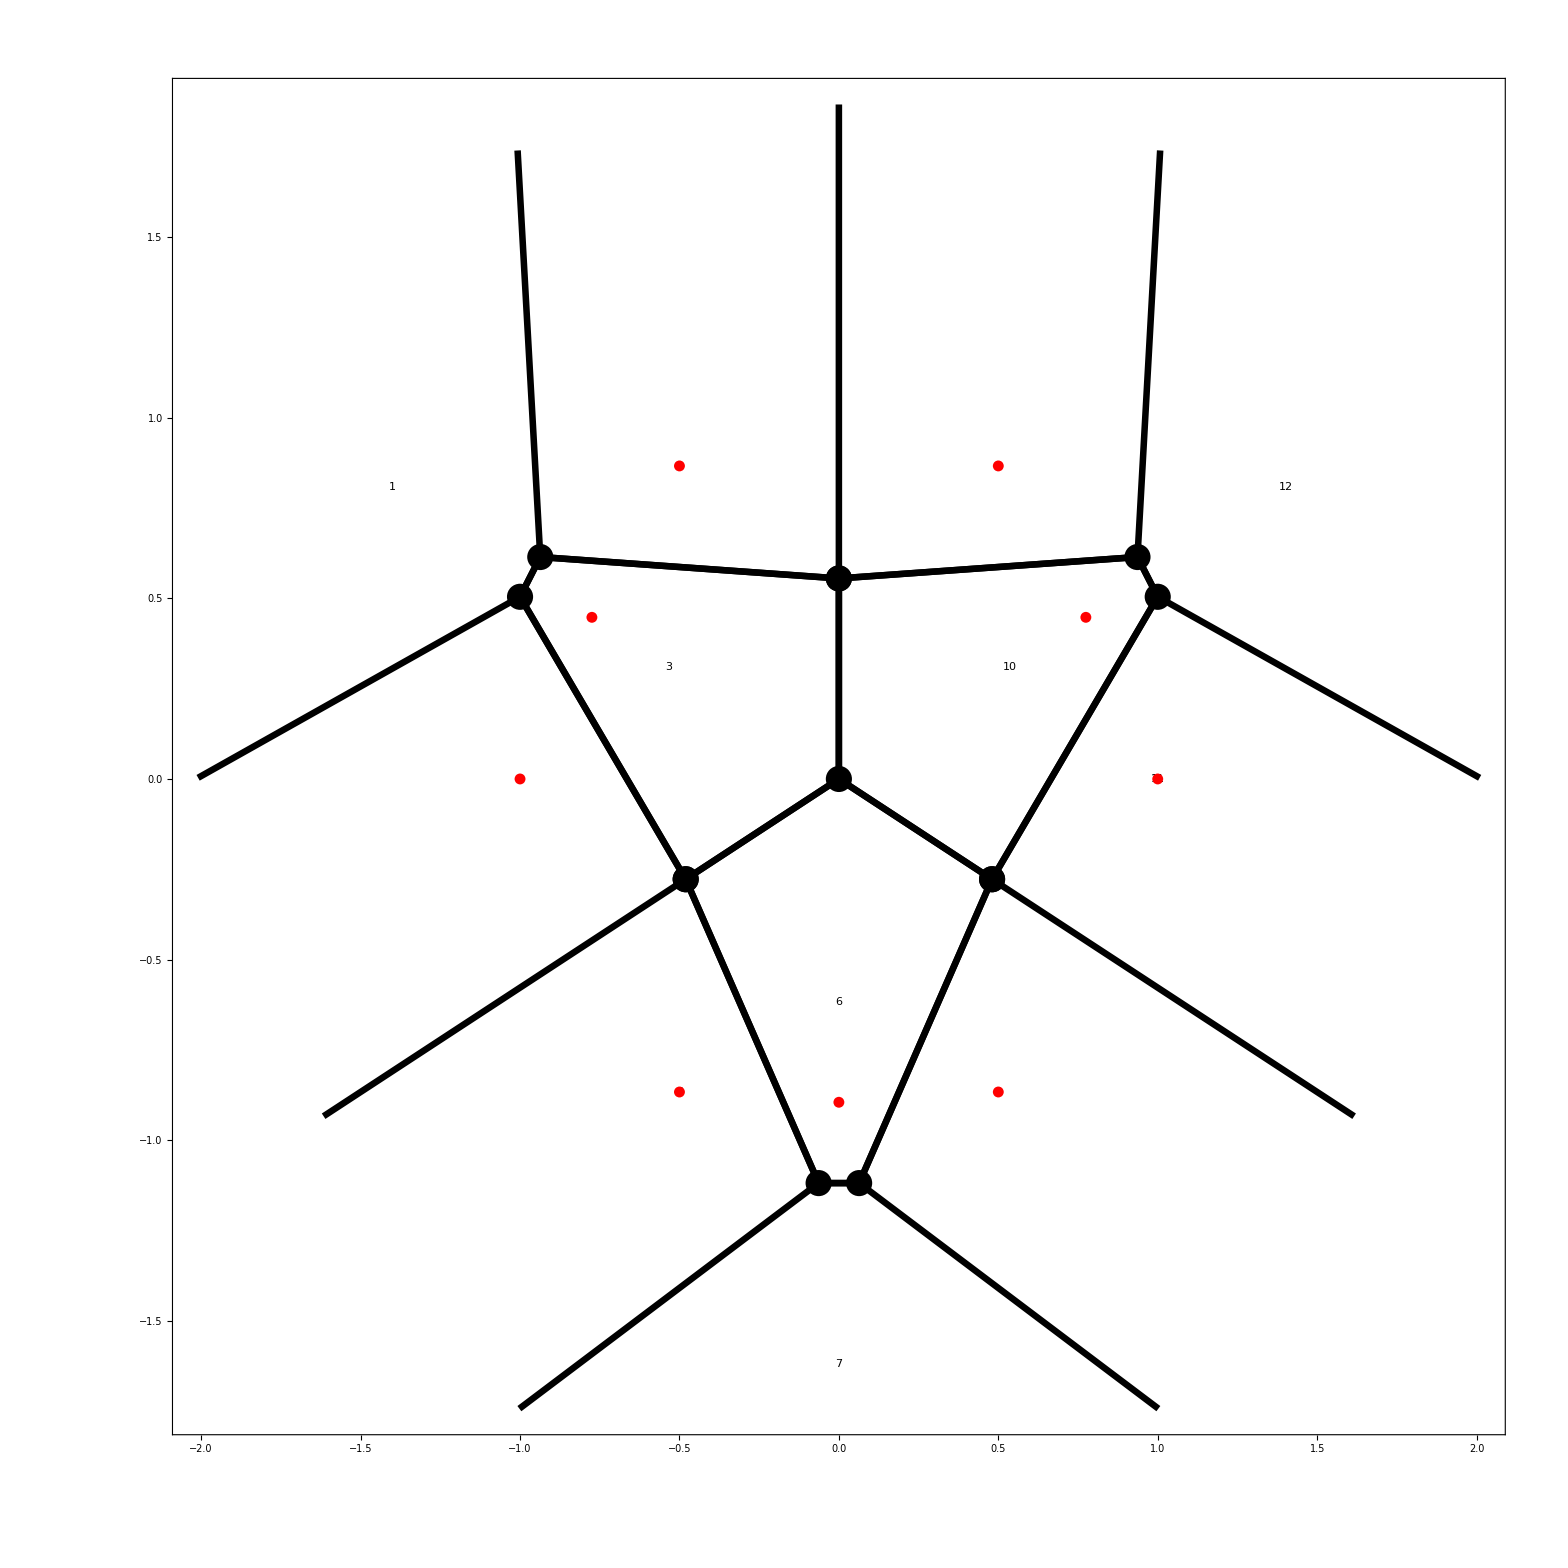

```mathematica
g1=Show[{
DiagramPlot[a0],
Graphics[{Red,PointSize[.005],Point[a]}]
},PlotRange->All,Frame->True,ImageSize->{2000,2000}]
```

```mathematica
(*g2=Show[Graphics3D[{Red,PointSize[0.0375/3],Point/@pts}],Axes->True,ImageSize->{2000,2000},ViewPoint->{5,5,5}]*)
```

```mathematica
(*(* Voronoi diagram*)
g1=Show[{
DiagramPlot[a0,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[a0]}]
},PlotRange->All,Frame->True,PlotRangeClipping->True,ImageSize->1000]
(* 3d projection of polyhedron*)*)
```

```mathematica
(* convex hull: MathWorld Library*)
<<ConvexHull`
```

```mathematica
hull0=ConvexHull3D[pts];
```

```mathematica
Length[hull0]
```

14

```mathematica
hull1=Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{}],{i,Length[hull0]}]];
```

```mathematica
hull3=Show[{g2,Graphics3D[{hull0,hull={Opacity[0.5],hull1}},ImageSize->{2000,2000},Boxed->False,Background->Black,ViewPoint->Right]},ImageSize->{2000,2000},Boxed->False,Background->Black,ViewPoint->{2,2,2}]
```

-Graphics3D-

```mathematica
Export["z12_363_2ndPolynomial12_convex_Hull_grid.jpg",GraphicsGrid[{{g1,g2},{ga,hull3}},ImageSize->{4000,4000}]]
```

z12_363_2ndPolynomial12_convex_Hull_grid.jpg

```mathematica
gg2=Show[hull3,ImageSize->{2000,2000},AspectRatio->1,ViewPoint->Above,Background->Black];
```

```mathematica
gg3=Show[hull3,ImageSize->{2000,2000},AspectRatio->1,ViewPoint->{1.3, -2.4, 2.},Background->Black];
```

```mathematica
gg4=Show[hull3,ImageSize->{2000,2000},AspectRatio->1,ViewPoint->Front,Background->Black];
```

```mathematica
Export["z12_363_2ndPolynomial12_grid.jpg",GraphicsGrid[{{hull3,gg2},{gg3,gg4}},ImageSize->{4000,4000}]]
```

z12_363_2ndPolynomial12_grid.jpg

```mathematica
Export["z12_363_2ndPolynomial12.stl",hull3]
```

z12_363_2ndPolynomial12.stl

```mathematica
model =Import["z12_363_2ndPolynomial12.stl"]
prt=Printout3D[model,"z12_363_2ndPolynomial12_stl_prt.stl"]
```

-Graphics3D-

```mathematica
(*end*)
```